## Devoir 1 (5 points) Remettre avant le 6 juin minuit par courriel à meunier@iro.umontreal.ca ***Votre nom ici***

### Question 1 (0.5 point): Mesurer le epsilon machine de votre ordinateur

### Solution

```mathematica
eps=1.0
```

1.

```mathematica
While[(1.0+eps)>1.0,eps=eps/2.0]
```

```mathematica
eps
```

1.42109×10^-14

On a divisé une fois de trop

```mathematica
eps*2
```

2.84217×10^-14

```mathematica
1.0+eps
```

1.

### Question 2 (1 point): Écrire un programme pour calculer la constante mathématique e = 2.718… à partir de la définition suivante: e =lim_(x→∞) (1+1/n)^n Plus précisément, utiliser n = 10^k avec k = 1,2,…,20. Déterminer l’erreur absolue de ces approximations en les comparant à la valeur de la fonction E de Mathematica. Tracer un graphique de l’erreur en fonction du Log[n] (ou k). Est-ce que l’erreur diminue toujours avec une augmentation de la valeur de n? Expliquer en terme d’erreur de troncature (série tronquée) et d’erreur d’arrondie.

### Solution

```mathematica
N[E,15]
```

2.71828182845905

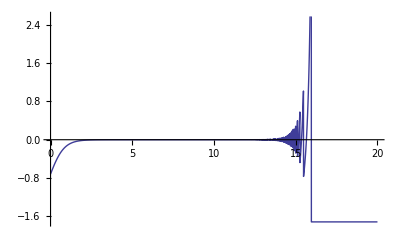

```mathematica
Plot[(1.+1/10^k)^(10^k)-E,{k,0,20}]
```

À compléter...
Non, l’erreur ne diminue pas toujours avec une augmentation de la valeur de n.
En terme d’erreur de troncature, nous avons constaté que notre graphique de l’erreur devient stable après 16.
En ce qui concerne l’erreur de l’arrondie, nous avons remarqué que l’erreur ne diminue pas toujours avec une augmentation de la valeur de n.

### Question 3 (1 point): Solutionner le système Ax = b avec la méthode de Gauss pour A = (1 | 2 | 3 4 | 5 | 6 7 | 8 | 10) et b = (1 1 1) sans pivotage. Vérifier vos résultats.Bonus: 1 point avec pivotage.

### Solution

```mathematica
a={{1,2,3},{4,5,6},{7,8,10}}
```

{{1,2,3},{4,5,6},{7,8,10}}

```mathematica
b={1,1,1}
```

{1,1,1}

```mathematica
n=3
```

3

```mathematica
For[k=1,k<n,k++,
For[i=k+1,i≤n,i++,
facteur=a[[i,k]]/a[[k,k]];
For[j=k+1,j≤n,j++,
a[[i,j]]=a[[i,j]]-facteur*a[[k,j]];
];
b[[i]]=b[[i]]-facteur*b[[k]];
];
]
```

```mathematica
a//MatrixForm
```

(1 | 2 | 3
4 | -3 | -6
7 | -6 | 1)

```mathematica
b
```

{1,-3,0}

```mathematica
u={{1,2,3},{0,-3,-6},{0,0,1}}
```

{{1,2,3},{0,-3,-6},{0,0,1}}

```mathematica
x=Inverse[u].b
```

{-1,1,0}

```mathematica
a={{1,2,3},{4,5,6},{7,8,10}}
```

{{1,2,3},{4,5,6},{7,8,10}}

```mathematica
a.x
```

{1,1,1}

```mathematica
LUDecomposition[a][[1]]//MatrixForm
```

(1 | 2 | 3
4 | -3 | -6
7 | 2 | 1)

```mathematica
gauss[A_,B_]:=Module[{facteur,n,a,b},
a=A;
b=B;
n=Dimensions[a][[1]];
For[k=1,k<n,k++,
For[i=k+1,i≤n-1,i++,
facteur=a[[i,k]]/a[[k,k]];
For[j=k+1,j≤n,j++,
a[[i,j]]=a[[i,j]]-facteur*a[[k,j]];
];
b[[i]]=b[[i]]-facteur*b[[k]];
];
];
{a,b}]
```

```mathematica
a={{1,2,3},{4,5,6},{7,8,10}}
```

{{1,2,3},{4,5,6},{7,8,10}}

```mathematica
b={1,1,1}
```

{1,1,1}

```mathematica
gauss[a,b]
Ux=y
U=({{1, 2, 3}, {4, -3, -6}, {7, -6, 1}})
y={1,-3,0}
ReplacePart[{{1,2,3},{4,-3,-6},{7,-6,1}},{i_,j_}/;i>j->0]
```

{{{1,2,3},{4,-3,-6},{7,8,10}},{1,-3,1}}

```mathematica
{1,-3,0}
```

```mathematica
x3:0/10
  x2:(-3-(0*-6))/-3
  x1:(1-(1*2))/1
```

x3:0

x2:1

x1:-1

À compléter avec la substitution arrière...pour obtenir la solution x directement avec la fonction gauss...

### Question 4 (1 point): Étude de la Matrice de Hilbert H dont les éléments sont définis comme h_ij = 1/(i+j-1). Par exemple la matrice 2 x 2 vaut (1 | 1/2 1/2 | 1/3). (a) Pour n = 2,3,…Calculer b = Hx où x est un vecteur avec tous les éléments égalent à 1. Ensuite utiliser un algorithme de votre choix pour solutionner le problème Hx = b afin d’obtenir une solution approximative x’. Enfin calculer la norme (à votre choix) du résidu r = b - Hx ainsi que l’erreur absolue |x-x’|. À partir de quelle valeur de n est-ce que l’erreur relative atteint 100% (c-à-d que la solution ne contient plus aucun chiffre significatif)? (b) Calculer l’inverse de cette matrice (quel que soit n) avec une méthode (numérique) de votre choix. Tester la validité de cet inverse en calculant le produit de AA^-1 qui devrait donner la matrice identité. Pour cela calculer la norme 1 ou ∞ de la matrice d’erreur soit || AA^-1 - I ||. Tracer un graphique « erreur vs. n ». Estimer le conditionnement (norme 1 ou ∞) de la matrice de Hilbert pour les différentes valeurs de n utilisées précédemment. Tracer un graphique « conditionnement vs. n ». Discuter vos résultats.

### Solution

```mathematica
h=N[HilbertMatrix[10]]
Dimensions@h
```

{{1.,0.5,0.333333,0.25,0.2,0.166667,0.142857,0.125,0.111111,0.1},{0.5,0.333333,0.25,0.2,0.166667,0.142857,0.125,0.111111,0.1,0.0909091},{0.333333,0.25,0.2,0.166667,0.142857,0.125,0.111111,0.1,0.0909091,0.0833333},{0.25,0.2,0.166667,0.142857,0.125,0.111111,0.1,0.0909091,0.0833333,0.0769231},{0.2,0.166667,0.142857,0.125,0.111111,0.1,0.0909091,0.0833333,0.0769231,0.0714286},{0.166667,0.142857,0.125,0.111111,0.1,0.0909091,0.0833333,0.0769231,0.0714286,0.0666667},{0.142857,0.125,0.111111,0.1,0.0909091,0.0833333,0.0769231,0.0714286,0.0666667,0.0625},{0.125,0.111111,0.1,0.0909091,0.0833333,0.0769231,0.0714286,0.0666667,0.0625,0.0588235},{0.111111,0.1,0.0909091,0.0833333,0.0769231,0.0714286,0.0666667,0.0625,0.0588235,0.0555556},{0.1,0.0909091,0.0833333,0.0769231,0.0714286,0.0666667,0.0625,0.0588235,0.0555556,0.0526316}}

{10,10}

```mathematica
MatrixForm[h].x
```

(1. | 0.5 | 0.333333 | 0.25 | 0.2 | 0.166667 | 0.142857 | 0.125 | 0.111111 | 0.1
0.5 | 0.333333 | 0.25 | 0.2 | 0.166667 | 0.142857 | 0.125 | 0.111111 | 0.1 | 0.0909091
0.333333 | 0.25 | 0.2 | 0.166667 | 0.142857 | 0.125 | 0.111111 | 0.1 | 0.0909091 | 0.0833333
0.25 | 0.2 | 0.166667 | 0.142857 | 0.125 | 0.111111 | 0.1 | 0.0909091 | 0.0833333 | 0.0769231
0.2 | 0.166667 | 0.142857 | 0.125 | 0.111111 | 0.1 | 0.0909091 | 0.0833333 | 0.0769231 | 0.0714286
0.166667 | 0.142857 | 0.125 | 0.111111 | 0.1 | 0.0909091 | 0.0833333 | 0.0769231 | 0.0714286 | 0.0666667
0.142857 | 0.125 | 0.111111 | 0.1 | 0.0909091 | 0.0833333 | 0.0769231 | 0.0714286 | 0.0666667 | 0.0625
0.125 | 0.111111 | 0.1 | 0.0909091 | 0.0833333 | 0.0769231 | 0.0714286 | 0.0666667 | 0.0625 | 0.0588235
0.111111 | 0.1 | 0.0909091 | 0.0833333 | 0.0769231 | 0.0714286 | 0.0666667 | 0.0625 | 0.0588235 | 0.0555556
0.1 | 0.0909091 | 0.0833333 | 0.0769231 | 0.0714286 | 0.0666667 | 0.0625 | 0.0588235 | 0.0555556 | 0.0526316).{1,1,1,1,1,1,1,1,1,1}

```mathematica
Inverse[h].h//MatrixForm
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,0.5,0.333333,0.25,0.2,0.166667,0.142857,0.125,0.111111,0.1},«8»,{0.1,0.0909091,0.0833333,0.0769231,0.0714286,0.0666667,0.0625,0.0588235,0.0555556,0.0526316}} may contain significant numerical errors.

(1. | 1.45519×10^-11 | 1.45519×10^-11 | 1.16415×10^-10 | -7.27596×10^-11 | 1.23691×10^-10 | 3.63798×10^-11 | -5.82077×10^-11 | 0. | 8.00355×10^-11
9.31323×10^-9 | 1. | -6.51926×10^-9 | 4.65661×10^-9 | 3.72529×10^-9 | 8.3819×10^-9 | -6.51926×10^-9 | 1.11759×10^-8 | 6.51926×10^-9 | -2.79397×10^-9
-2.98023×10^-7 | 2.38419×10^-7 | 1. | 2.08616×10^-7 | -4.47035×10^-8 | 4.47035×10^-8 | 1.19209×10^-7 | -2.23517×10^-7 | 8.9407×10^-8 | 1.3411×10^-7
-1.19209×10^-6 | -9.53674×10^-7 | -2.38419×10^-7 | 0.999998 | 0. | -1.90735×10^-6 | -3.57628×10^-7 | -9.53674×10^-7 | -1.19209×10^-7 | -1.78814×10^-6
3.8147×10^-6 | -9.53674×10^-6 | 6.67572×10^-6 | -2.86102×10^-6 | 0.999995 | 9.53674×10^-7 | 9.53674×10^-7 | -0.0000123978 | -6.67572×10^-6 | 0.0000114441
0.0000114441 | 3.8147×10^-6 | 0.0000190735 | 0. | 7.62939×10^-6 | 1.00003 | -3.8147×10^-6 | 0.000043869 | 0.0000362396 | -0.0000152588
7.62939×10^-6 | 0.0000686646 | 7.62939×10^-6 | 3.8147×10^-6 | 0.0000152588 | 0.0000190735 | 0.999981 | -0.0000495911 | -0.0000267029 | 0.0000228882
-0.0000610352 | -0.0000686646 | -0.000118256 | -0.0000228882 | 7.62939×10^-6 | 0.0000419617 | -0.0000419617 | 1.00005 | 0.0000190735 | -0.0000228882
3.8147×10^-6 | -0.0000228882 | -0.0000190735 | -0.0000190735 | -0.0000228882 | -0.0000209808 | -0.0000190735 | -0.0000209808 | 0.999985 | 7.62939×10^-6
-3.8147×10^-6 | -0.0000104904 | -5.24521×10^-6 | 4.76837×10^-7 | -1.90735×10^-6 | -4.76837×10^-7 | -1.90735×10^-6 | -1.90735×10^-6 | -2.38419×10^-6 | 0.999996)

```mathematica
x={1,1,1,1,1,1,1,1,1,1}
b=h .x
```

{1,1,1,1,1,1,1,1,1,1}

{2.92897,2.01988,1.60321,1.3468,1.16823,1.0349,0.930729,0.846695,0.777251,0.718771}

```mathematica
gauss[h, b]
```

```mathematica
t={{{1.,0.5,0.3333333333333333,0.25,0.2,0.16666666666666666,0.14285714285714285,0.125,0.1111111111111111,0.1},{0.5,0.08333333333333331,0.08333333333333334,0.07500000000000001,0.06666666666666665,0.05952380952380952,0.053571428571428575,0.048611111111111105,0.04444444444444445,0.04090909090909091},{0.3333333333333333,0.08333333333333334,0.005555555555555522,0.00833333333333329,0.009523809523809504,0.0099206349206349,0.009920634920634892,0.009722222222222215,0.009427609427609403,0.009090909090909066},{0.25,0.07500000000000001,0.00833333333333329,0.00035714285714287357,0.0007142857142857194,0.000992063492063499,0.001190476190476207,0.001325757575757567,0.0014141414141414163,0.001468531468531483},{0.2,0.06666666666666665,0.009523809523809504,0.0007142857142857176,0.000022675736961467324,0.00005668934240368262,0.00009276437847871013,0.0001262626262626917,0.00015540015540023997,0.0001798201798202427},{0.16666666666666666,0.05952380952380952,0.009920634920634906,0.0009920634920634868,0.000056689342403691296,1.4315490504818174*^-6,4.29464715166213*^-6,8.093758093620409*^-6,0.000012333345666458895,0.00001665001664981244},{0.14285714285714285,0.053571428571428575,0.009920634920634885,0.0011904761904762105,0.000092764378478711,4.294647151666385*^-6,9.009749236431395*^-8,3.1534122355354906*^-7,6.727279441136888*^-7,1.1352284059808372*^-6},{0.125,0.048611111111111105,0.009722222222222215,0.0013257575757575583,0.0001262626262627021,8.093758093625342*^-6,3.1534122355283416*^-7,5.659970607161749*^-9,2.2639882063151857*^-8,5.393618987142274*^-8},{0.1111111111111111,0.04444444444444445,0.00942760942760941,0.001414141414141406,0.00015540015540024344,0.000012333345666490554,6.727279440740274*^-7,2.263988211294257*^-8,3.551362553328898*^-10,1.5981116503797872*^-9},{0.1,0.04090909090909091,0.009090909090909066,0.001468531468531483,0.00017982017982023533,0.000016650016649857164,1.1352284059341149*^-6,5.393618991849829*^-8,1.5981118119434075*^-9,2.2266569430696655*^-11}},{2.9289682539682538,0.5553932178932182,0.07149470899470844,0.007462398712398982,0.0006336124193269035,0.00004280331661232089,2.2133950654792056*^-6,8.223604328178183*^-8,1.9532470308437125*^-9}}
```

{{{1.,0.5,0.333333,0.25,0.2,0.166667,0.142857,0.125,0.111111,0.1},{0.5,0.0833333,0.0833333,0.075,0.0666667,0.0595238,0.0535714,0.0486111,0.0444444,0.0409091},{0.333333,0.0833333,0.00555556,0.00833333,0.00952381,0.00992063,0.00992063,0.00972222,0.00942761,0.00909091},{0.25,0.075,0.00833333,0.000357143,0.000714286,0.000992063,0.00119048,0.00132576,0.00141414,0.00146853},{0.2,0.0666667,0.00952381,0.000714286,0.0000226757,0.0000566893,0.0000927644,0.000126263,0.0001554,0.00017982},{0.166667,0.0595238,0.00992063,0.000992063,0.0000566893,1.43155×10^-6,4.29465×10^-6,8.09376×10^-6,0.0000123333,0.00001665},{0.142857,0.0535714,0.00992063,0.00119048,0.0000927644,4.29465×10^-6,9.00975×10^-8,3.15341×10^-7,6.72728×10^-7,1.13523×10^-6},{0.125,0.0486111,0.00972222,0.00132576,0.000126263,8.09376×10^-6,3.15341×10^-7,5.65997×10^-9,2.26399×10^-8,5.39362×10^-8},{0.111111,0.0444444,0.00942761,0.00141414,0.0001554,0.0000123333,6.72728×10^-7,2.26399×10^-8,3.55136×10^-10,1.59811×10^-9},{0.1,0.0409091,0.00909091,0.00146853,0.00017982,0.00001665,1.13523×10^-6,5.39362×10^-8,1.59811×10^-9,2.22666×10^-11}},{2.92897,0.555393,0.0714947,0.0074624,0.000633612,0.0000428033,2.2134×10^-6,8.2236×10^-8,1.95325×10^-9}}

```mathematica
t[[2]]//MatrixForm
```

(2.92897
0.555393
0.0714947
0.0074624
0.000633612
0.0000428033
2.2134×10^-6
8.2236×10^-8
1.95325×10^-9
2.22675×10^-11)

Dot::dotsh: Tensors {{1.,0.5},{0.5,0.333333}} and {-1,1,0} have incompatible shapes.

À compléter...

### Question 5 (1 point): Implémenter en Mathematica un LU modifié avec permutation qui conservera des 1 sur la diagonale de U plutôt que L à partir du LU obtenu avec Mathematica. Valider votre algorithme avec la matrice (2 | 4 | -2 4 | 9 | -3 -2 | -3 | 7) vue au cours. Expliquer comment vous procédez.

### Solution

```mathematica
LUDecomposition[{{2,4,-2},{4,9,-3},{-2,-3,7}}]
```

{{{2,4,-2},{2,1,1},{-1,1,4}},{1,2,3},1}

À compléter...

### Question 6 (0.5 point): Démontrer expérimentalement avec Mathematica et la matrice (1 | 1 | 1 1 | 1 | 1 1 | 1 | 1) que la factorisation LU peut exister même si la matrice est singulière.

### Solution

```mathematica
a=ConstantArray[1,{3,3}]
```

{{1,1,1},{1,1,1},{1,1,1}}

```mathematica
LUDecomposition[a]
```

LUDecomposition::sing: Matrix {{1, 1, 1}, {1, 1, 1}, {1, 1, 1}} is singular.

```mathematica
{{{1,1,1},{1,0,0},{1,0,0}},{1,2,3},1}
```

```mathematica
l={{1,0,0},{1,1,0},{1,0,1}}
```

```mathematica
{{1,0,0},{1,1,0},{1,0,1}}//MatrixForm
```

(1 | 0 | 0
1 | 1 | 0
1 | 0 | 1)

```mathematica
u={{1,1,1},{0,0,0},{0,0,0}}
```

{{1,1,1},{0,0,0},{0,0,0}}

```mathematica
l.u
```

```mathematica
{{1,1,1},{1,1,1},{1,1,1}}
```

```mathematica
l={{1,1,1},{1,0,0},{1,0,0}} SparseArray[{i_,j_}/;j<i->1,{3,3}]+IdentityMatrix[3]
```

```mathematica
{{1,0,0},{1,1,0},{1,0,1}}//MatrixForm
```

```mathematica
({{1, 0, 0}, {1, 1, 0}, {1, 0, 1}})

u={{1,1,1},{1,0,0},{1,0,0}}SparseArray[{i_,j_}/;j≥i->1,{3,3}]//MatrixForm
```

{{1,0,0},{1,1,0},{1,0,1}}

(1 | 1 | 1
0 | 0 | 0
0 | 0 | 0)